```mathematica
Cos[-μ*t  + π/2 + δ]
```

```mathematica
ω = 2*π*18
```

36 π

```mathematica
U = 2π
h=0
For[i=0, i<30, i++, h += U*Cos[-i*ω*x + π/2 + .25]];
s=NDSolve[{ⅈ*y'[x]==h*y[x] ,y[0]==1},y,{x,0,30}]
```

2 π

0

{{y→InterpolatingFunction[{{0., 30.}}, <>]}}

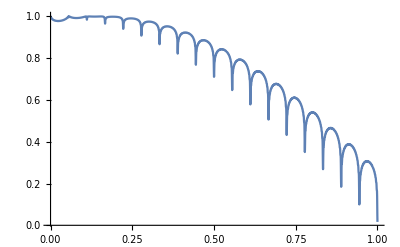

```mathematica
Plot[Re[Evaluate[y[x]/.s]],{x,0,1},PlotRange->All]
```

```mathematica
s
```

{{y→InterpolatingFunction[…]}}

```mathematica
1/.s
```

{1}

```mathematica
Re[Evaluate[y[1]/.s][[1]]]
```

ReplaceAll::reps: {s} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Re[y[1]]

```mathematica
data=Import["~/repos/single_site_addressability/final_notebooks/test.csv","CSV"];
```

```mathematica
sim[dd_]:= Module[{d}, d=dd; 
ω = 2*π*18;
U = 2π*1;
h=0;
a = .1;
end = π/(a*2*U);
For[i=0, i≤12, i++, h += U*Cos[-i*ω*x - π/2 + a*d]];
s=NDSolve[{ⅈ*y'[x]==h*y[x] ,y[0]==1/Sqrt[2]},y,{x,0,end}, MaxSteps->Infinity];
up = {Re[Evaluate[y[end]/.s][[1]]], Im[Evaluate[y[end]/.s][[1]]]};
s=NDSolve[{ⅈ*y'[x]==-h*y[x] ,y[0]==1/Sqrt[2]},y,{x,0,end}, MaxSteps->Infinity];
down = {Re[Evaluate[y[end]/.s][[1]]], Im[Evaluate[y[end]/.s][[1]]]};
{up, down}
]
Map[sim, data]
```

{{{0.00185241,-0.707105},{0.00185241,0.707105}}}

```mathematica
{{0.00181819,-0.707105},{0.00181819,0.707105}},{{0.247383,-0.662422},{0.247383,0.662422}},{{0.598607,-0.376391},{0.598607,0.376391}},{{0.698678,-0.108853},{0.698678,0.108853}},{{0.706872,-0.018219},{0.706872,0.018219}},{{0.707076,-0.00659546},{0.707076,0.00659546}},{{0.707071,-0.00723517},{0.707071,0.00723517}},{{0.707107,-0.000645717},{0.707107,0.000645717}},{{0.706854,-0.0189134},{0.706854,0.0189134}},{{0.697566,-0.115769},{0.697566,0.115769}},{{0.592407,-0.386077},{0.592407,0.386077}},{{0.247383,-0.662422},{0.247383,0.662422}},{{0.0334266,-0.706317},{0.0334266,0.706317}},{{0.247382,-0.662423},{0.247382,0.662423}},{{0.592403,-0.386082},{0.592403,0.386082}},{{0.247382,-0.662423},{0.247382,0.662423}},{{0.0334266,-0.706317},{0.0334266,0.706317}},{{0.29116,-0.644381},{0.29116,0.644381}},{{0.613396,-0.351776},{0.613396,0.351776}},{{0.702044,-0.0844687},{0.702044,0.0844687}},{{0.364264,-0.606064},{0.364264,0.606064}},{{0.129748,-0.695102},{0.129748,0.695102}},{{0.364266,-0.606062},{0.364266,0.606062}},{{0.613396,-0.351775},{0.613396,0.351775}},{{0.702044,-0.0844693},{0.702044,0.0844693}},{{0.706873,-0.0182211},{0.706873,0.0182211}},{{0.707076,-0.00660378},{0.707076,0.00660378}},{{0.70707,-0.00723563},{0.70707,0.00723563}},{{0.707065,0.0077152},{0.707065,-0.0077152}},{{0.707066,-0.00762967},{0.707066,0.00762967}},{{0.70702,0.0111222},{0.70702,-0.0111222}},{{0.706901,-0.017094},{0.706901,0.017094}},{{0.70702,0.0111222},{0.70702,-0.0111222}},{{0.707053,-0.00876229},{0.707053,0.00876229}},{{0.707086,0.00552506},{0.707086,-0.00552506}},{{0.707096,-0.0038777},{0.707096,0.0038777}},{{0.707107,-0.000634106},{0.707107,0.000634106}},{{0.706855,-0.0189015},{0.706855,0.0189015}},{{0.698676,-0.108854},{0.698676,0.108854}},{{0.598607,-0.376391},{0.598607,0.376391}},{{0.291148,-0.644386},{0.291148,0.644386}},{{0.697567,-0.115769},{0.697567,0.115769}},{{0.706809,-0.0205458},{0.706809,0.0205458}},{{0.707105,-0.00209395},{0.707105,0.00209395}},{{0.707105,-0.00203014},{0.707105,0.00203014}},{{0.707086,0.00552506},{0.707086,-0.00552506}},{{0.707066,-0.00762967},{0.707066,0.00762967}},{{0.707065,0.0077152},{0.707065,-0.0077152}},{{0.707096,-0.0038777},{0.707096,0.0038777}},{{0.707105,-0.00209395},{0.707105,0.00209395}},{{0.706855,-0.0189015},{0.706855,0.0189015}},{{0.697567,-0.115769},{0.697567,0.115769}},{{0.598607,-0.376391},{0.598607,0.376391}},{{0.698676,-0.108854},{0.698676,0.108854}},{{0.706873,-0.0182211},{0.706873,0.0182211}},{{0.707107,-0.000634106},{0.707107,0.000634106}},{{0.70707,-0.00723563},{0.70707,0.00723563}},{{0.707076,-0.00660378},{0.707076,0.00660378}},{{0.702044,-0.0844693},{0.702044,0.0844693}},{{0.613396,-0.351775},{0.613396,0.351775}},{{0.291148,-0.644386},{0.291148,0.644386}},{{0.129748,-0.695102},{0.129748,0.695102}},{{0.29116,-0.644381},{0.29116,0.644381}},{{0.598607,-0.376391},{0.598607,0.376391}},{{0.697566,-0.115769},{0.697566,0.115769}},{{0.70681,-0.0205388},{0.70681,0.0205388}},{{0.707105,-0.00209358},{0.707105,0.00209358}},{{0.707097,-0.00386971},{0.707097,0.00386971}},{{0.707065,0.00771405},{0.707065,-0.00771405}},{{0.707065,-0.00762702},{0.707065,0.00762702}},{{0.707086,0.0055243},{0.707086,-0.0055243}},{{0.707105,-0.00203062},{0.707105,0.00203062}},{{0.707105,-0.00209358},{0.707105,0.00209358}},{{0.706854,-0.0189134},{0.706854,0.0189134}},{{0.698678,-0.108853},{0.698678,0.108853}},{{0.613396,-0.351776},{0.613396,0.351776}},{{0.364264,-0.606064},{0.364264,0.606064}},{{0.702044,-0.0844687},{0.702044,0.0844687}},{{0.706872,-0.018219},{0.706872,0.018219}},{{0.707107,-0.000645717},{0.707107,0.000645717}},{{0.707097,-0.00386971},{0.707097,0.00386971}},{{0.707086,0.0055243},{0.707086,-0.0055243}},{{0.707054,-0.00876172},{0.707054,0.00876172}},{{0.70702,0.0111193},{0.70702,-0.0111193}},{{0.706901,-0.0170909},{0.706901,0.0170909}},{{0.70702,0.0111193},{0.70702,-0.0111193}},{{0.707065,-0.00762702},{0.707065,0.00762702}},{{0.707065,0.00771405},{0.707065,-0.00771405}},{{0.707071,-0.00723517},{0.707071,0.00723517}},{{0.707076,-0.00659546},{0.707076,0.00659546}},{{0.364266,-0.606062},{0.364266,0.606062}}
```

{{{0.000430033,-0.707107},{0.000430033,0.707107}},{{0.246777,-0.662647},{0.246777,0.662647}},{{0.598573,-0.376444},{0.598573,0.376444}},{{0.698678,-0.108853},{0.698678,0.108853}},{{0.706872,-0.018221},{0.706872,0.018221}},{{0.707076,-0.0065953},{0.707076,0.0065953}},{{0.70707,-0.00723619},{0.70707,0.00723619}},{{0.707106,-0.000634619},{0.707106,0.000634619}},{{0.706854,-0.018902},{0.706854,0.018902}},{{0.697565,-0.115771},{0.697565,0.115771}},{{0.592364,-0.38614},{0.592364,0.38614}},{{0.246777,-0.662647},{0.246777,0.662647}},{{0.0321505,-0.706375},{0.0321505,0.706375}},{{0.246777,-0.662647},{0.246777,0.662647}},{{0.592365,-0.38614},{0.592365,0.38614}},{{0.246777,-0.662647},{0.246777,0.662647}},{{0.0321505,-0.706375},{0.0321505,0.706375}},{{0.290654,-0.644609},{0.290654,0.644609}},{{0.613371,-0.351819},{0.613371,0.351819}},{{0.702043,-0.0844695},{0.702043,0.0844695}},{{0.36392,-0.606269},{0.36392,0.606269}},{{0.128798,-0.695278},{0.128798,0.695278}},{{0.36392,-0.606269},{0.36392,0.606269}},{{0.613371,-0.351819},{0.613371,0.351819}},{{0.702043,-0.0844698},{0.702043,0.0844698}},{{0.706872,-0.018221},{0.706872,0.018221}},{{0.707076,-0.0065953},{0.707076,0.0065953}},{{0.70707,-0.00723595},{0.70707,0.00723595}},{{0.707065,0.00771989},{0.707065,-0.00771989}},{{0.707066,-0.00762713},{0.707066,0.00762713}},{{0.707019,0.0111224},{0.707019,-0.0111224}},{{0.7069,-0.0170936},{0.7069,0.0170936}},{{0.707019,0.0111224},{0.707019,-0.0111224}},{{0.707052,-0.00876258},{0.707052,0.00876258}},{{0.707085,0.00552425},{0.707085,-0.00552425}},{{0.707096,-0.00386909},{0.707096,0.00386909}},{{0.707106,-0.000634613},{0.707106,0.000634613}},{{0.706854,-0.0189016},{0.706854,0.0189016}},{{0.698678,-0.108853},{0.698678,0.108853}},{{0.598573,-0.376444},{0.598573,0.376444}},{{0.290653,-0.644609},{0.290653,0.644609}},{{0.697565,-0.11577},{0.697565,0.11577}},{{0.706808,-0.0205386},{0.706808,0.0205386}},{{0.707104,-0.00209396},{0.707104,0.00209396}},{{0.707104,-0.00203067},{0.707104,0.00203067}},{{0.707085,0.00552425},{0.707085,-0.00552425}},{{0.707066,-0.00762713},{0.707066,0.00762713}},{{0.707065,0.00771989},{0.707065,-0.00771989}},{{0.707096,-0.00386909},{0.707096,0.00386909}},{{0.707104,-0.00209396},{0.707104,0.00209396}},{{0.706854,-0.0189016},{0.706854,0.0189016}},{{0.697565,-0.11577},{0.697565,0.11577}},{{0.598573,-0.376444},{0.598573,0.376444}},{{0.698678,-0.108853},{0.698678,0.108853}},{{0.706872,-0.018221},{0.706872,0.018221}},{{0.707106,-0.000634613},{0.707106,0.000634613}},{{0.70707,-0.00723595},{0.70707,0.00723595}},{{0.707076,-0.0065953},{0.707076,0.0065953}},{{0.702043,-0.0844698},{0.702043,0.0844698}},{{0.613371,-0.351819},{0.613371,0.351819}},{{0.290653,-0.644609},{0.290653,0.644609}},{{0.128798,-0.695278},{0.128798,0.695278}},{{0.290654,-0.644609},{0.290654,0.644609}},{{0.598573,-0.376444},{0.598573,0.376444}},{{0.697565,-0.115771},{0.697565,0.115771}},{{0.706808,-0.0205389},{0.706808,0.0205389}},{{0.707104,-0.00209402},{0.707104,0.00209402}},{{0.707096,-0.00386944},{0.707096,0.00386944}},{{0.707065,0.00772036},{0.707065,-0.00772036}},{{0.707066,-0.00762691},{0.707066,0.00762691}},{{0.707085,0.00552421},{0.707085,-0.00552421}},{{0.707104,-0.00203106},{0.707104,0.00203106}},{{0.707104,-0.00209402},{0.707104,0.00209402}},{{0.706854,-0.018902},{0.706854,0.018902}},{{0.698678,-0.108853},{0.698678,0.108853}},{{0.613371,-0.351819},{0.613371,0.351819}},{{0.36392,-0.606269},{0.36392,0.606269}},{{0.702043,-0.0844695},{0.702043,0.0844695}},{{0.706872,-0.018221},{0.706872,0.018221}},{{0.707106,-0.000634619},{0.707106,0.000634619}},{{0.707096,-0.00386944},{0.707096,0.00386944}},{{0.707085,0.00552421},{0.707085,-0.00552421}},{{0.707052,-0.00876222},{0.707052,0.00876222}},{{0.707019,0.0111227},{0.707019,-0.0111227}},{{0.7069,-0.0170911},{0.7069,0.0170911}},{{0.707019,0.0111227},{0.707019,-0.0111227}},{{0.707066,-0.00762691},{0.707066,0.00762691}},{{0.707065,0.00772036},{0.707065,-0.00772036}},{{0.70707,-0.00723619},{0.70707,0.00723619}},{{0.707076,-0.0065953},{0.707076,0.0065953}},{{0.36392,-0.606269},{0.36392,0.606269}}}

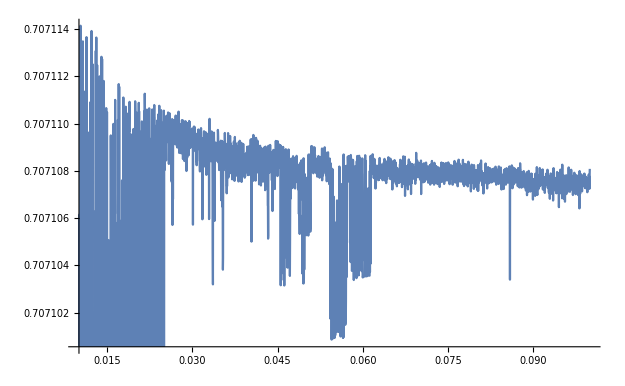

```mathematica
Plot[Norm[sim[data[[1]], a][[1]]],{a, .01, .1}]
```

```mathematica
Norm[{1,2}]
```

√5

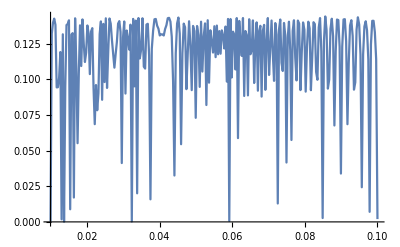

```mathematica
sim[dd_, b_]:= Module[{d, a}, d = dd[[1]]; a=b; 
ω = 2*π*18;
U = 2π*1;
h=0;
end = π/(a*2*U);
For[i=0, i≤10, i++, h += U*Cos[-i*ω*x - π/2 + a*d]];
s=NDSolve[{ⅈ*y'[x]==h*y[x] ,y[0]==1/Sqrt[2]},y,{x,0,end}, MaxSteps->Infinity];
up = {Re[Evaluate[y[end]/.s][[1]]], Im[Evaluate[y[end]/.s][[1]]]}]
Plot[sim[data26[[1]], z][[1]], {z, .01, .1}, PlotPoints->5]
```